```mathematica
(*Note there is something weird about this notebook - evaluate three times and it should work*)
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis"];
filesEinsteinPot={"T_dudl_meam_4685","T_dudl_meam_4730","T_dudl_meam_4759","T_dudl_meam_4801","T_dudl_meam_4850"};
TdUdL=Table[ReadList[filesEinsteinPot[[i]],{Number, Number}],{i,1,5}];
temps={300,760,1900,2500,3200,3805};
lambda=Table[i/10,{i,0,10}]//N;
vols={4.685,4.730,4.759,4.801,4.850};
```

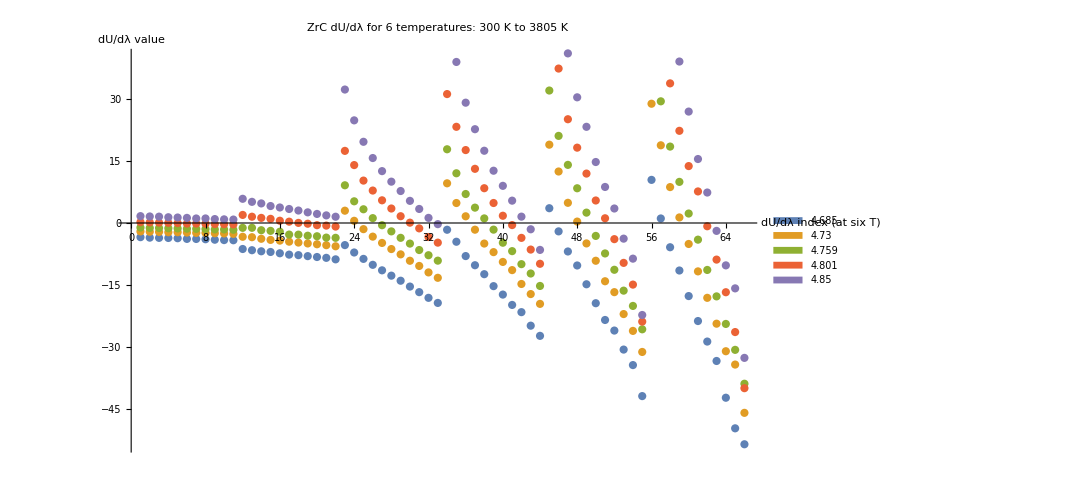

```mathematica
(*dUdL plot all temps all vols*)
ListPlot[Table[Transpose[TdUdL[[i]]][[2]],{i,1,5}],PlotLabel->"ZrC dU/dλ for 6 temperatures: 300 K to 3805 K",AxesLabel->{"dU/dλ index \n(at six T)","dU/dλ value"},ImageSize->800,PlotLegends->SwatchLegend[vols]]
```

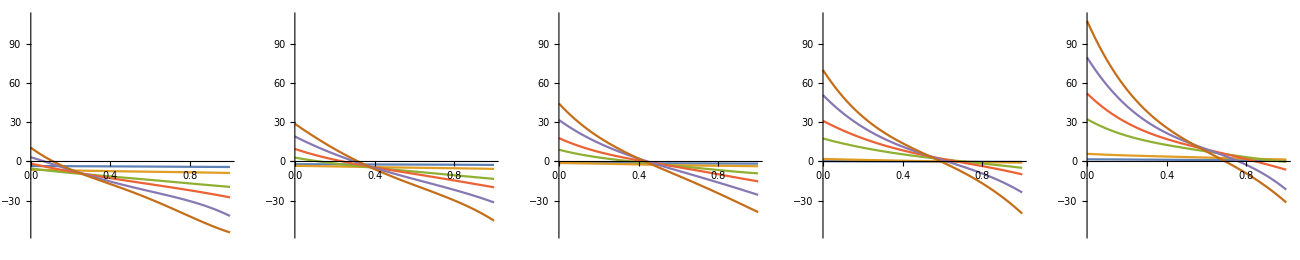

```mathematica
(*dUdL polynomial fits plot all temps all vols*)
GraphicsGrid[{Table[Plot[Evaluate@Table[Fit[Partition[TdUdL[[vol]],11][[temp]],{1,x,x^2,x^3,x^4},x],{temp,1,6}],{x,0,1},PlotRange->{{0,1},{-55,110}}],{vol,1,5}]},ImageSize->1300]
```

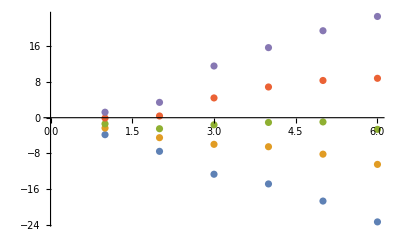

```mathematica
(*Fah = int dUdL polynomial fits at all vols and all temps*)
FahData=Integrate[Table[Table[Fit[Partition[TdUdL[[vol]],11][[temp]],{1,x,x^2,x^3,x^4},x],{temp,1,6}],{vol,1,5}],{x,0,1}];
ListPlot@FahData
```

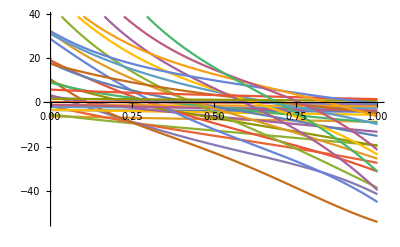

```mathematica
dudlFit=Table[Table[Fit[Partition[TdUdL[[vol]],11][[temp]],{1,x,x^2,x^3,x^4},x],{temp,1,6}],{vol,1,5}];
Plot[Evaluate@dudlFit,{x,0,1}]
```

```mathematica
(*Data format for dudlFits : dudlFit[[vol]][[temp]] *)
```

```mathematica
(*Perfect Fah Data*)
FahData//TableForm
```

-3.81143 | -7.54809 | -12.686 | -14.8639 | -18.7054 | -23.3822
-2.32337 | -4.48527 | -5.97792 | -6.51571 | -8.18144 | -10.4777
-1.37785 | -2.47588 | -1.59493 | -1.06442 | -0.948908 | -2.61856
-0.0762672 | 0.385152 | 4.43411 | 6.89367 | 8.35227 | 8.841
1.23554 | 3.44112 | 11.6014 | 15.7243 | 19.5159 | 22.7188

```mathematica
diffhalfVals=0.5(({dudlLambdaFits4685,dudlLambdaFits4801,dudlLambdaFits4850}/.x->1)+({dudlLambdaFits4685,dudlLambdaFits4801,dudlLambdaFits4850}/.x->0));
```

```mathematica
(*0.5*(L=0 + L=1) approx Fah Data*)
FahDataL01=0.5((dudlFit/.x->0)+(dudlFit/.x->1));
FahDataL01//TableForm
```

-3.8108 | -7.55297 | -12.3578 | -14.4932 | -19.1628 | -21.7798
-2.34024 | -4.47654 | -5.15403 | -5.04715 | -6.07427 | -8.18894
-1.3768 | -2.38144 | -0.0271696 | 1.3672 | 3.11331 | 2.81941
-0.0595526 | 0.542084 | 6.35571 | 10.6085 | 13.5347 | 15.0558
1.24489 | 3.68527 | 16.0028 | 22.809 | 28.9509 | 38.0327

```mathematica
(*  L=0.5 approx Fah Data*)
FahDataL05=dudlFit/.x->0.5;
FahDataL05//TableForm
```

-3.79048 | -7.59275 | -12.7336 | -15.0632 | -19.1923 | -22.7673
-2.31721 | -4.53684 | -6.27668 | -7.02049 | -9.35522 | -12.1938
-1.37442 | -2.6035 | -2.01936 | -1.79735 | -2.59837 | -4.47577
-0.0895829 | 0.318914 | 3.48475 | 5.02628 | 5.89303 | 6.45907
1.22544 | 3.37899 | 10.0379 | 12.8285 | 14.9405 | 15.9202

```mathematica
plotinfos={PlotLabel->"Anharmonic free energy (ΔA) and thermodynamic integration approximations",AxesLabel->{"ΔA","ΔA \n approximation"},ImageSize->700}
```

{PlotLabel→Anharmonic free energy (ΔA) and thermodynamic integration approximations,AxesLabel→{ΔA,ΔA 
 approximation},ImageSize→700}

```mathematica
Manipulate[Show[ListPlot[{FahData[[volume]],dudlFit[[volume]]/.x->u,FahDataL05[[volume]],FahDataL01[[volume]]},PlotLegends->SwatchLegend[{"Exact","=λ: Mean-value theorem"  Evaluate[MVTforVolumes[[volume]]],"⟨V^anh-V^qha⟩_(λ = 0.5)","0.5(⟨V^anh-V^qha⟩_(λ = 1) + ⟨V^anh-V^qha⟩_(λ = 0) )"}],Evaluate@plotinfos],ListPlot[{FahData[[volume]],dudlFit[[volume]]/.x->u,FahDataL05[[volume]],FahDataL01[[volume]]},Joined->True],PlotRange->All],{{u,Evaluate[MVTforVolumes[[volume]]],"λ for mean-value theorem"},0,1}]/.volume->1
```

Part::pkspec1: The expression volume cannot be used as a part specification.

```mathematica
Manipulate[Show[ListPlot[{FahData[[volume]],dudlFit[[volume]]/.x->u,FahDataL05[[volume]],FahDataL01[[volume]]},PlotLegends->SwatchLegend[{"Exact","=λ: Mean-value theorem"  Evaluate[MVTforVolumes[[volume]]],"⟨V^anh-V^qha⟩_(λ = 0.5)","0.5(⟨V^anh-V^qha⟩_(λ = 1) + ⟨V^anh-V^qha⟩_(λ = 0) )"}],Evaluate@plotinfos],ListPlot[{FahData[[volume]],dudlFit[[volume]]/.x->u,FahDataL05[[volume]],FahDataL01[[volume]]},Joined->True],PlotRange->All],{{u,Evaluate[MVTforVolumes[[volume]]],"λ for mean-value theorem"},0,1}]/.volume->2
```

Part::pkspec1: The expression volume cannot be used as a part specification.

```mathematica
(*Vol=4.759Angstrom*)
Manipulate[Show[ListPlot[{FahData[[volume]],dudlFit[[volume]]/.x->u,FahDataL05[[volume]],FahDataL01[[volume]]},PlotLegends->SwatchLegend[{"Exact","=λ: Mean-value theorem"  Evaluate[MVTforVolumes[[volume]]],"⟨V^anh-V^qha⟩_(λ = 0.5)","0.5(⟨V^anh-V^qha⟩_(λ = 1) + ⟨V^anh-V^qha⟩_(λ = 0) )"}],Evaluate@plotinfos],ListPlot[{FahData[[volume]],dudlFit[[volume]]/.x->u,FahDataL05[[volume]],FahDataL01[[volume]]},Joined->True],PlotRange->All],{{u,Evaluate[MVTforVolumes[[volume]]],"λ for mean-value theorem"},0,1}]/.volume->3
```

Part::pkspec1: The expression volume cannot be used as a part specification.

```mathematica
(*Vol=4.801Angstrom*)
Manipulate[Show[ListPlot[{FahData[[volume]],dudlFit[[volume]]/.x->u,FahDataL05[[volume]],FahDataL01[[volume]]},PlotLegends->SwatchLegend[{"Exact","=λ: Mean-value theorem"  Evaluate[MVTforVolumes[[volume]]],"⟨V^anh-V^qha⟩_(λ = 0.5)","0.5(⟨V^anh-V^qha⟩_(λ = 1) + ⟨V^anh-V^qha⟩_(λ = 0) )"}],Evaluate@plotinfos],ListPlot[{FahData[[volume]],dudlFit[[volume]]/.x->u,FahDataL05[[volume]],FahDataL01[[volume]]},Joined->True],PlotRange->All],{{u,Evaluate[MVTforVolumes[[volume]]],"λ for mean-value theorem"},0,1}]/.volume->4
```

Part::pkspec1: The expression volume cannot be used as a part specification.

```mathematica
(*Vol=4.850Angstrom*)
Manipulate[Show[ListPlot[{FahData[[volume]],dudlFit[[volume]]/.x->u,FahDataL05[[volume]],FahDataL01[[volume]]},PlotLegends->SwatchLegend[{"Exact","=λ: Mean-value theorem"  Evaluate[MVTforVolumes[[volume]]],"⟨V^anh-V^qha⟩_(λ = 0.5)","0.5(⟨V^anh-V^qha⟩_(λ = 1) + ⟨V^anh-V^qha⟩_(λ = 0) )"}],Evaluate@plotinfos],ListPlot[{FahData[[volume]],dudlFit[[volume]]/.x->u,FahDataL05[[volume]],FahDataL01[[volume]]},Joined->True],PlotRange->All],{{u,Evaluate[MVTforVolumes[[volume]]],"λ for mean-value theorem"},0,1}]/.volume->5
```

Part::pkspec1: The expression volume cannot be used as a part specification.

0.49976-0.67371 a+4.83377 a^2-20.3401 a^3

0.49878-0.412248 a

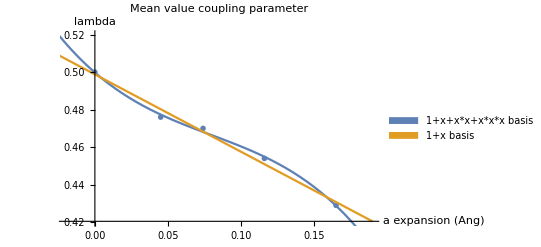

```mathematica
(*Mean value theorem solutions for each volume*)
MVTforVolumes={0.5,0.476,0.47,0.454,0.429};
lambda3=Fit[Transpose[{vols-vols[[1]],MVTforVolumes}],{1,a,a^2,a^3},a]
lambda1=Fit[Transpose[{vols-vols[[1]],MVTforVolumes}],{1,a},a]

Show[ListPlot[Transpose[{vols-vols[[1]],MVTforVolumes}],PlotRange->{{-0.02,0.19},{0.42,0.52}},PlotLabel->"Mean value coupling parameter",PlotMarkers->X,AxesLabel->{"a expansion (Ang)","lambda"}],Plot[{Evaluate@lambda3/.a->x,Evaluate@lambda1/.a->x},{x,-0.05,0.19},PlotLegends->SwatchLegend[{"1+x+x*x+x*x*x  basis","1+x  basis"}]]]
```

```mathematica
lambda1/.x->0.1
```

0.49878-0.412248 a

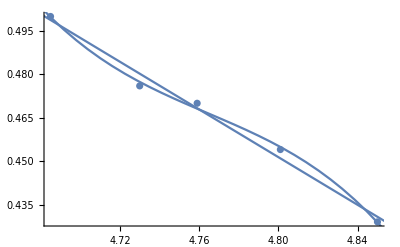

```mathematica
Show[ListPlot@Transpose[{vols,MVTforVolumes}],Plot[Evaluate@Fit[Transpose[{vols,MVTforVolumes}],{1,x,x^2,x^3},x],{x,4.6,4.9}],Plot[Evaluate@Fit[Transpose[{vols,MVTforVolumes}],{1,x},x],{x,4.6,4.9}]]
```

```mathematica
Manipulate[Show[ListPlot[{Transpose@{FahData[[volume]],FahData[[volume]]},Transpose@{FahData[[volume]],dudlFit[[volume]]/.x->u},Transpose@{FahData[[volume]],FahDataL05[[volume]]},Transpose@{FahData[[volume]],FahDataL01[[volume]]}},PlotLegends->SwatchLegend[{"Exact","=λ: Mean-value theorem"  Evaluate[MVTforVolumes[[volume]]],"⟨V^anh-V^qha⟩_(λ = 0.5)","0.5(⟨V^anh-V^qha⟩_(λ = 1) + ⟨V^anh-V^qha⟩_(λ = 0) )"}],Evaluate@plotinfos],ListPlot[{Transpose@{FahData[[volume]],FahData[[volume]]},Transpose@{FahData[[volume]],dudlFit[[volume]]/.x->u},Transpose@{FahData[[volume]],FahDataL05[[volume]]},Transpose@{FahData[[volume]],FahDataL01[[volume]]}},Joined->True],PlotRange->All],{{u,Evaluate[MVTforVolumes[[volume]]],"λ for mean-value theorem"},0,1}]/.volume->5
```

Part::pkspec1: The expression volume cannot be used as a part specification.

```mathematica
data=Flatten[{#1->#2}&@@@Transpose[{vols-vols[[1]],MVTforVolumes}]]
```

{0.→0.5,0.045→0.476,0.074→0.47,0.116→0.454,0.165→0.429}

```mathematica
p=Predict[data,Method->"GaussianProcess"]
```

PredictorFunction[…]

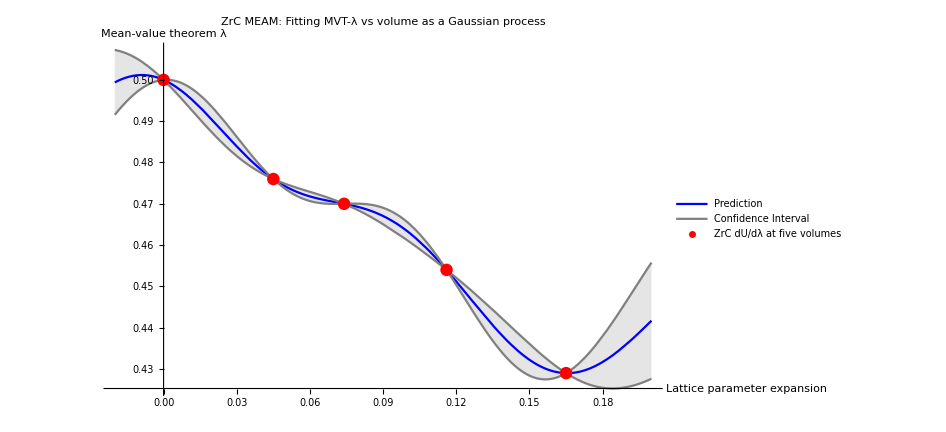

```mathematica
Show[Plot[{p[x],p[x]+StandardDeviation[p[x,"Distribution"]],p[x]-StandardDeviation[p[x,"Distribution"]]},{x,-0.02,0.2},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->False,PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"}],ListPlot[List@@@data,PlotStyle->Red,PlotLegends->{"ZrC dU/dλ at five volumes"}],AxesLabel->{"Lattice parameter\n expansion","Mean-value\n theorem λ"},ImageSize->700,PlotLabel->"ZrC MEAM: Fitting MVT-λ vs volume as a Gaussian process"]
```

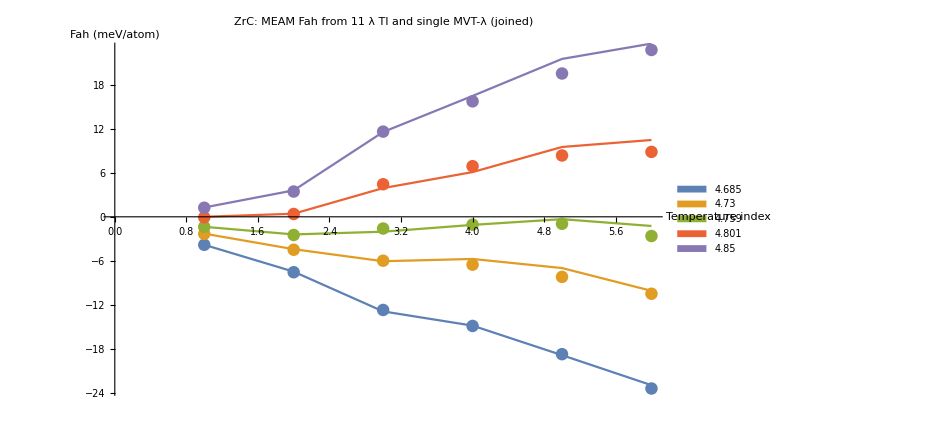

```mathematica
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis"];MVTintAll=Transpose@ReadList["MVT_intall",{Number, Number,Number,Number,Number}];
Show[ListPlot[FahData,AxesLabel->{"Temperature \nindex","Fah (meV/atom)"},PlotLabel->"ZrC: MEAM Fah from 11 λ TI and single MVT-λ (joined)"],ListPlot[MVTintAll,Joined->True,PlotLegends->SwatchLegend[vols]],ImageSize->700]
```

```mathematica
FahData[[5]]
```

{1.23554,3.44112,11.6014,15.7243,19.5159,22.7188}

```mathematica
MVTintAll
```

{{-3.81,-7.47,-12.88,-14.82,-18.84,-22.93},{-2.29,-4.41,-6.05,-5.74,-6.98,-10.08},{-1.36,-2.4,-2.03,-1.1,-0.32,-1.25},{0.,0.42,3.91,6.09,9.51,10.46},{1.27,3.6,11.55,16.46,21.5,23.59}}

```mathematica
gauss=Predict[Flatten[{#1->#2}&@@@MVTintAll],Method->"GaussianProcess"]
```

PredictorFunction[…]

PredictorFunction::mlincfttp: Incompatible variable type (Numerical) and variable value (x).

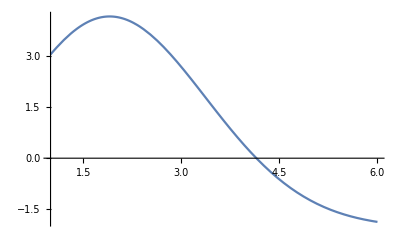

```mathematica
Plot[gauss[x],{x,1,6}]
```

```mathematica
eV2meVat=1000/64;
SetDirectory["/Volumes/MicroSD/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis/UP_sample"];
filesEpotminusEperf={"TI_EpotminusEperf_3__4759","TI_EpotminusEperf_4__4801","TI_EpotminusEperf_5__4850"};
EpotminusEperf=Table[ReadList[filesEpotminusEperf[[i]],{Number, Number,Number, Number,Number, Number,Number, Number,Number}],{i,1,3}];
filesUPF={"TI_UP_F_3__4759","TI_UP_F_4__4801","TI_UP_F_5__4850"};
UPF=Table[ReadList[filesUPF[[i]],{Number, Number,Number, Number,Number, Number}],{i,1,3}];
filesUPE0={"TI_UP_E0_3__4759","TI_UP_E0_4__4801","TI_UP_E0_5__4850"};
UPE0=Table[ReadList[filesUPE0[[i]],{Number, Number,Number, Number,Number, Number}],{i,1,3}];
```

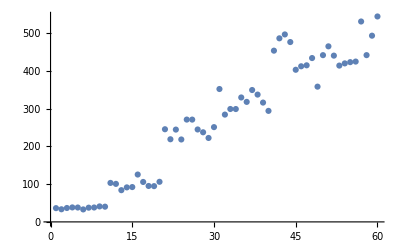

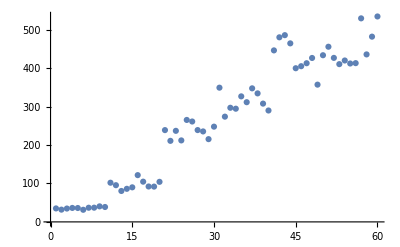

```mathematica
ListPlot@Transpose[EpotminusEperf[[3]]][[5]]
ListPlot@Flatten@Table[Table[Take[eV2meVat*(Transpose[UPE0[[vol]]][[i]]-UPE0[[vol]][[1]][[i]]),-10],{i,1,6}],{vol,1,3}][[3]]
```

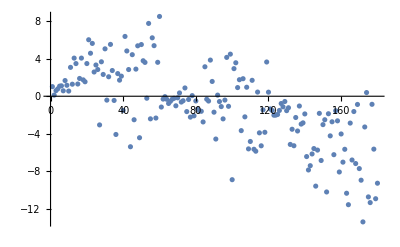

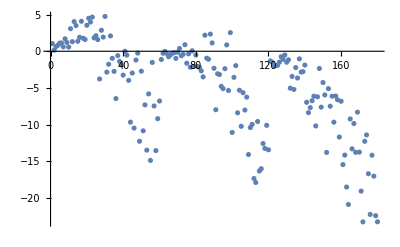

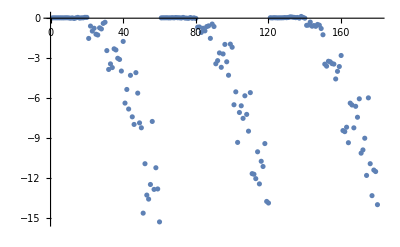

```mathematica
hf=Table[Table[Take[eV2meVat*(Transpose[UPF[[vol]]][[i]]-UPF[[vol]][[1]][[i]]),-10],{i,1,6}],{vol,1,3}];
h=Table[Table[Take[eV2meVat*(Transpose[UPE0[[vol]]][[i]]-UPE0[[vol]][[1]][[i]]),-10],{i,1,6}],{vol,1,3}];
l=Table[Table[Partition[Transpose[EpotminusEperf[[j]]][[5]],10][[i]],{i,1,6}],{j,1,3}];
ListPlot[Flatten@(h-l)]
ListPlot[Flatten@(hf-l)]
ListPlot[Flatten@(hf-h)]
```

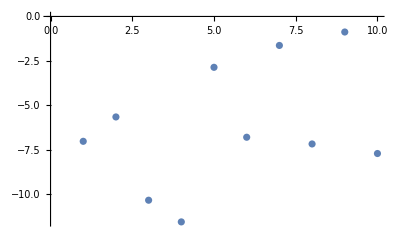

```mathematica
ListPlot[(h-l)[[3]][[5]]]
```

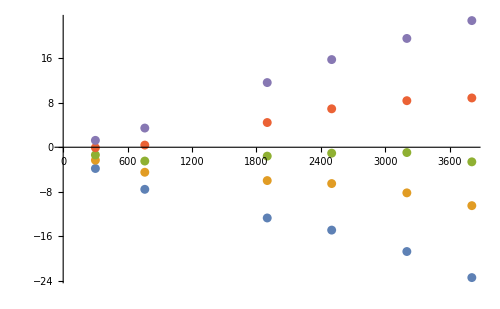

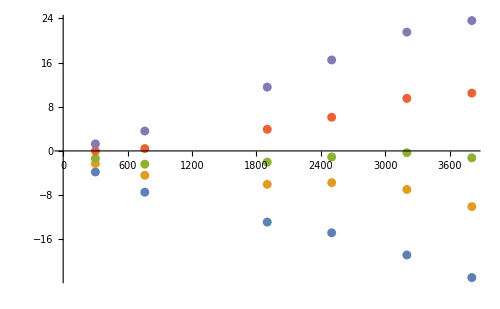

```mathematica
ListPlot[Table[Transpose@{temps,FahData[[i]]},{i,1,5}],ImageSize->500]
ListPlot[Table[Transpose@{temps,MVTintAll[[i]]},{i,1,5}],ImageSize->500]
```

```mathematica
hm=Table[Mean@Transpose@h[[i]],{i,1,3}];
hfm=Table[Mean@Transpose@hf[[i]],{i,1,3}];
lm=Table[Mean@Transpose@l[[i]],{i,1,3}];
ListPlot[{hm[[1]]-lm[[1]]},PlotLegends->SwatchLegend[{"high","low"}]];
```

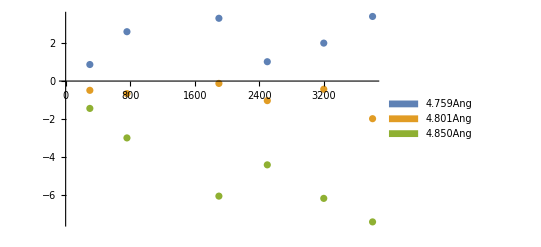

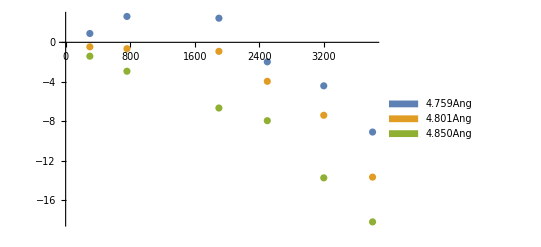

```mathematica
ListPlot[Table[Transpose@{temps,(hm-lm)[[i]]},{i,1,3}],PlotLegends->SwatchLegend[{"4.759Ang","4.801Ang","4.850Ang"}]]
ListPlot[Table[Transpose@{temps,(hfm-lm)[[i]]},{i,1,3}],PlotLegends->SwatchLegend[{"4.759Ang","4.801Ang","4.850Ang"}]]
```

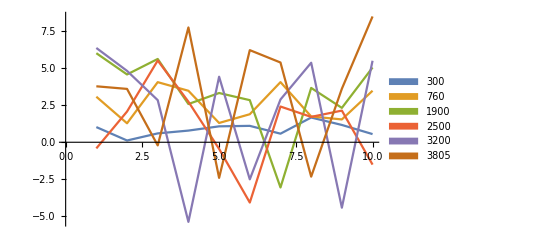

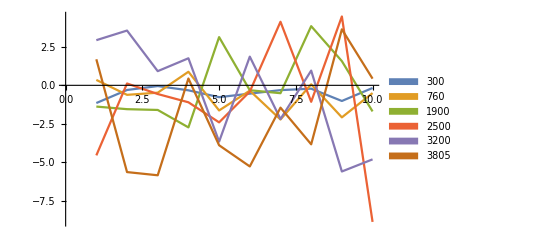

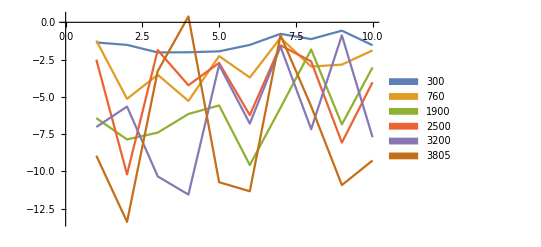

```mathematica
ListPlot[((h-l)[[1]]),Joined->True,PlotLegends->SwatchLegend[{"300","760","1900","2500","3200","3805"}]]
ListPlot[((h-l)[[2]]),Joined->True,PlotLegends->SwatchLegend[{"300","760","1900","2500","3200","3805"}]]
ListPlot[((h-l)[[3]]),Joined->True,PlotLegends->SwatchLegend[{"300","760","1900","2500","3200","3805"}]]
```

```mathematica
p=Predict[Flatten[{#1->#2}&@@@Transpose@{temps,MVTintAll[[1]]}],Method->"GaussianProcess"]
```

PredictorFunction[…]

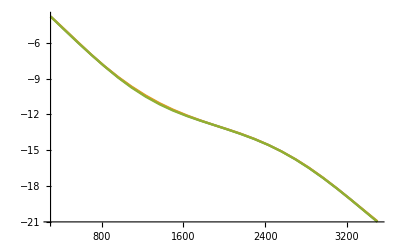

```mathematica
Plot[{p[x],p[x]+StandardDeviation[p[x,"Distribution"]],p[x]-StandardDeviation[p[x,"Distribution"]]},{x,300,3500},Exclusions->False,PerformanceGoal->"Speed"]
```

```mathematica
e
```

e

```mathematica
(h-l)[[2]][[1]]
```

{-1.15219,-0.303906,-0.0471875,-0.325156,-0.770156,-0.540469,-0.312344,-0.218281,-1.01859,-0.172031}

{{0,0},{300,0.867719},{760,2.59058},{1900,3.29453},{2500,1.01503},{3200,1.99155},{3805,3.39037}}

0.939171+0.000527524 x

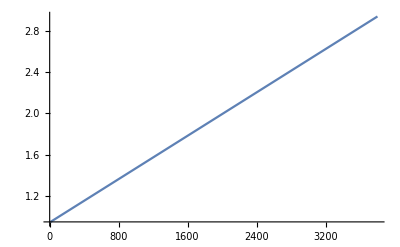

{{0,0},{300,-0.486031},{760,-0.659328},{1900,-0.124391},{2500,-1.02702},{3200,-0.427437},{3805,-1.97494}}

-0.130175-0.000303884 x

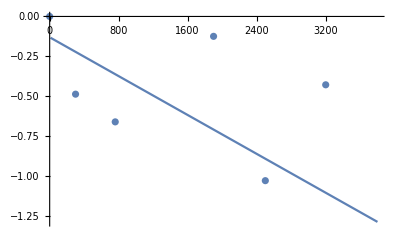

{{0,0},{300,-1.43567},{760,-2.98392},{1900,-6.03875},{2500,-4.39762},{3200,-6.15711},{3805,-7.3917}}

-0.999196-0.00171764 x

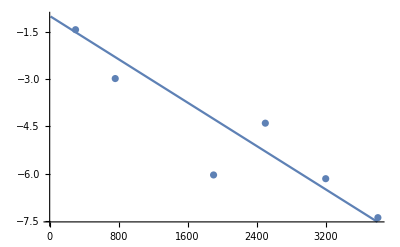

```mathematica
up4759=Partition[Flatten@{{0,0},Transpose@{temps,(hm-lm)[[1]]}},2]
fup4759=Fit[up4759,{1,x},x]
Show[Plot[fup4759,{x,10,3800}],ListPlot@up4801]
up4801=Partition[Flatten@{{0,0},Transpose@{temps,(hm-lm)[[2]]}},2]
fup4801=Fit[up4801,{1,x},x]
Show[Plot[fup4801,{x,10,3800}],ListPlot@up4801]
up4850=Partition[Flatten@{{0,0},Transpose@{temps,(hm-lm)[[3]]}},2]
fup4850=Fit[up4850,{1,x},x]
Show[Plot[fup4850,{x,10,3800}],ListPlot@up4850]
```

{{{0,0},{300,0.867719},{760,2.59058},{1900,3.29453},{2500,1.01503},{3200,1.99155},{3805,3.39037}},{{0,0},{300,-0.486031},{760,-0.659328},{1900,-0.124391},{2500,-1.02702},{3200,-0.427437},{3805,-1.97494}},{{0,0},{300,-1.43567},{760,-2.98392},{1900,-6.03875},{2500,-4.39762},{3200,-6.15711},{3805,-7.3917}}}

{0.664753+0.0011917 x-1.80393×10^-7 x^2,-0.372854+0.000283476 x-1.59529×10^-7 x^2,-0.47313-0.00299089 x+3.45817×10^-7 x^2}

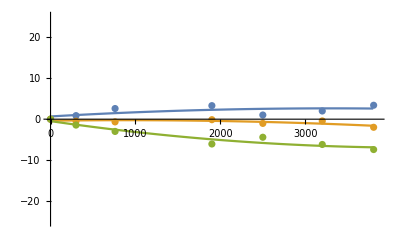

```mathematica
up=Table[Partition[Flatten@{{0,0},Transpose@{temps,(hm-lm)[[i]]}},2],{i,1,3}]
fup=Table[Fit[Partition[Flatten@{{0,0},Transpose@{temps,(hm-lm)[[i]]}},2],{1,x,x^2},x],{i,1,3}]
Show[Plot[fup,{x,10,3800},PlotRange->{{0,3850},{-25,25}}],ListPlot@up]
```

{{{0,0},{300,-3.81143},{760,-7.54809},{1900,-12.686},{2500,-14.8639},{3200,-18.7054},{3805,-23.3822}},{{0,0},{300,-2.32337},{760,-4.48527},{1900,-5.97792},{2500,-6.51571},{3200,-8.18144},{3805,-10.4777}},{{0,0},{300,-1.37785},{760,-2.47588},{1900,-1.59493},{2500,-1.06442},{3200,-0.948908},{3805,-2.61856}},{{0,0},{300,-0.0762672},{760,0.385152},{1900,4.43411},{2500,6.89367},{3200,8.35227},{3805,8.841}},{{0,0},{300,1.23554},{760,3.44112},{1900,11.6014},{2500,15.7243},{3200,19.5159},{3805,22.7188}}}

{-1.38273-0.00620903 x+1.72437×10^-7 x^2,-1.08763-0.00283211 x+1.40562×10^-7 x^2,-0.984356-0.000332913 x+2.72289×10^-8 x^2,-0.777579+0.00298304 x-8.25806×10^-8 x^2,-0.592515+0.00654634 x-9.12314×10^-8 x^2}

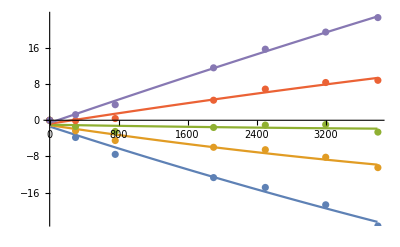

```mathematica
low=Table[Partition[Flatten@{{0,0},Transpose@{temps,FahData[[i]]}},2],{i,1,5}]
flow=Table[Fit[Partition[Flatten@{{0,0},Transpose@{temps,FahData[[i]]}},2],{1,x,x^2},x],{i,1,5}]
Show[Plot[flow,{x,10,3800}],ListPlot@low]
```

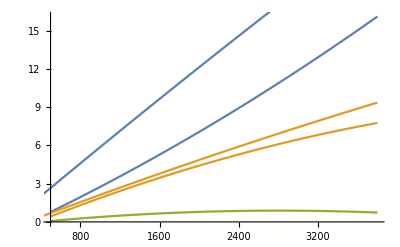

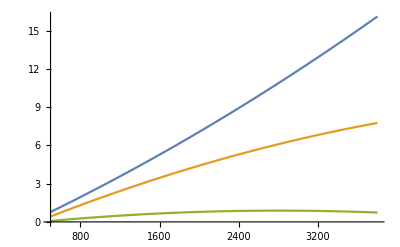

```mathematica
Show[Plot[{flow[[5]]+fup[[3]],flow[[4]]+fup[[2]],flow[[3]]+fup[[1]]},{x,500,3800}],Plot[{flow[[5]],flow[[4]],flow[[3]]},{x,10,3800}]]
Show[Plot[{flow[[5]]+fup[[3]],flow[[4]]+fup[[2]],flow[[3]]+fup[[1]]},{x,500,3800}]]
```